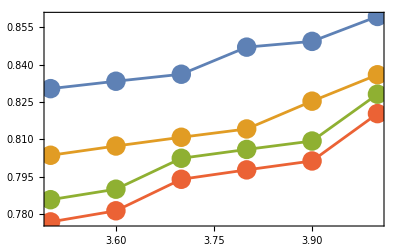

```mathematica
a={{3.5,93/(3.5×32)}, {3.6,96/(3.6×32)},{3.7,99/(3.7×32)},{3.8,103/(3.8×32)}, {3.9,106/(3.9×32)},{4.0,110/(4×32)}};
a2={{3.5,90/(3.5×32)}, {3.6,93/(3.6×32)},{3.7,96/(3.7×32)},{3.8,99/(3.8×32)}, {3.9,103/(3.9×32)},{4.0,107/(4×32)}};
a3={{3.5,88/(3.5×32)}, {3.6,91/(3.6×32)},{3.7,95/(3.7×32)},{3.8,98/(3.8×32)}, {3.9,101/(3.9×32)},{4.0,106/(4×32)}};
a4={{3.5,87/(3.5×32)}, {3.6,90/(3.6×32)},{3.7,94/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,105/(4×32)}};
ListPlot[{a,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True},LabelStyle->Directive[Black,36]]
```

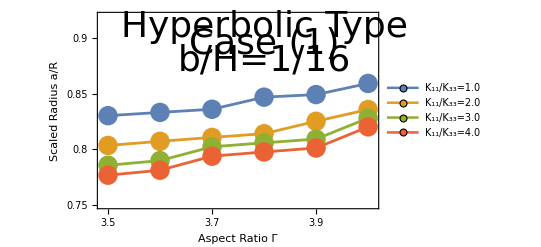

```mathematica
ListPlot[{a,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.75,0.80,0.85,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0.75,0.92}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{3.8,0.91}],Text[Style["Case (1)",Directive[Black,36]],{3.8,0.895}],Text[Style["b/H=1/16",Directive[Black,36]],{3.8,0.88}]}]
```

```mathematica
N[ⅇ^(0.14/0.4),9]
```

1.41907

```mathematica
N[ⅇ^(0.14/1),9]
```

1.15027

```mathematica
≈
```